# Intro to Fourier Analysis

## Basic Idea

There is an easily inverted linear transformation from ℂ^n to ℂ^n that decomposes a signal x∈ℂ^n into a very useful list y∈ℂ^n which describes the oscillations in the signal x.

This mapping described by a matrix F∈ℂ^(n×n) in all sorts of science and engineering to denoise and analyze real signals x∈ℝ^n.  The mapping is easy to describe in complex arithmetic and complicated in real arithmetic.  This is an example of the quote below from a famous French mathematician/scientist  https://en.wikipedia.org/wiki/Jacques_Hadamard

“It has been written that the shortest and best way between two truths of the real domain often passes through the imaginary one .”
Jacques Hadamard page number 123 which is p147 in the pdf below 
http://worrydream.com/refs/Hadamard%20-%20The%20psychology%20of%20invention%20in%20the%20mathematical%20field.pdf

The plan is to define the matrix F, explain how to interpret the complex Discrete Fourier Transform (DFT) y=F x for a real signal x∈ℝ^n, and later explain how the Fast Fourier Transform (FFT) can apply F to a vector x at a cost of O(n log_2(n)) flops.

### The Fourier Matrix F∈ℂ^(n×n)

The n×n Fourier Matrix is 
	F_(j,k)=1/(√n)ω^((j-1)*(k-1))
where θ=2π/n and ω=ⅇ^(θ ⅈ)=cos(θ)+ⅈ sin(θ).  As noted in the Wikipedia page (https://en.wikipedia.org/wiki/DFT_matrix) physicists, mathematicians, and engineers sometimes make different choices for the sign in ω=ⅇ^(±θ ⅈ) and scaling in this matrix.  You should check what the convention is in papers and software.  All that is going on if you see ω^(j*k) is that computer scientists (along with some engineers and scientists) like to start counting at zero instead of 1!

The definition above matches Mathematica.

```mathematica
n=6;θ=2π/n;ω=ⅇ^(θ ⅈ);F=Table[1/(√n)ω^((j-1)*(k-1)),{j,n},{k,n}];
TabView[{
"Def"->MatrixForm[F],
"Mma"->MatrixForm[FourierMatrix[n]],
"Difference"->MatrixForm[F-FourierMatrix[n]]
}]
```

123

Mathematicians like this normalized definition because in the inverse of F is just the conjugate (or since F is symmetric the conjugate transpose) of F. Mathematicians like the symmetry.

```mathematica
n=7;θ=2π/n;ω=ⅇ^(θ ⅈ);ωbar=ⅇ^(-θ ⅈ);
F=Table[1/(√n)ω^((j-1)*(k-1)),{j,n},{k,n}];
FInv=Table[1/(√n)ωbar^((j-1)*(k-1)),{j,n},{k,n}];
TabView[{
"F"->MatrixForm[F],
"F^-1"->MatrixForm[FInv],
"F.F^-1"->MatrixForm[FullSimplify[F.FInv]]
}]
```

123

Summary: 
The Fourier Matrix F is a symmetric matrix with an easily computed inverse.

### Why does anyone care about the Fourier Matrix F∈ℂ^(n×n)

Here is a clean wiggly signal

```mathematica
tp[θ_]:=5+ 3.2 Sin[2 θ ]+ 1.4 Cos[3 θ]- 2.3 Sin[5 θ]+ 6 Cos[13 θ] 
n=4356; F=N[FourierMatrix[n]];Δθ=2.0π/n;
x=Table[tp[θ],{θ, Δθ,2π,Δθ}]; 
f=F.x;
TabView[{
"x"->ListPlot[x],
"f"->ListPlot[{Re[f],Im[f]},DataRange->{0,n-1},PlotRange->All],
"f_low"->ListPlot[{Re[f],Im[f]},DataRange->{0,n-1},PlotRange->{{0,15},All},
PlotStyle->PointSize[Medium]],
"f_high"->ListPlot[{Re[f],Im[f]},DataRange->{0,n-1},PlotRange->{{n-15,n-1},All},
PlotStyle->PointSize[Medium]]
}]
```

1234

Here is a very noisy wiggly signal.  This is how signals get denoised.

```mathematica
tp[θ_]:=5+ 3.2 Sin[2 θ ]+ 1.4 Cos[3 θ]- 2.3 Sin[5 θ]+ 6 Cos[6 θ] +2 RandomReal[{-1,1}]
n=500; F=N[FourierMatrix[n]];Δθ=2.0π/n;
x=Table[tp[θ],{θ, Δθ,2π,Δθ}]; 
f=F.x;
fFilter=0.0*f;
fFilter⟦1;;7⟧=f⟦1;;7⟧;
fFilter⟦-6;;-1⟧=f⟦-6;;-1⟧;
xFilter=LinearSolve[F,fFilter];
TabView[{
"x"->ListPlot[x],
"f"->ListPlot[{Re[f],Im[f]},DataRange->{0,n-1},PlotRange->All],
"fFilter"->ListPlot[{Re[fFilter],Im[fFilter]},DataRange->{0,n-1},PlotRange->All],
"Im(xFilter)"->ListPlot[Im[xFilter]],
"Re(xFilter)"->ListPlot[Re[xFilter]],
"Fit"->ListPlot[{x,Re[xFilter]}]
}]
```

123456

Summary: 
The Discrete Fourier Transform (DFT) f=F.x shows the wiggle content in a signal.

The abs(f_i) gives how much of the signal is associated with "i-1" wiggles in the signal.

re(f_i) gives the amount of cosine present

im(f_i) gives the amount of sine present

Noise is typically high frequency.  the DFT is frequently used to denoise a signal.

### Frequency and the sound of music

Technical people do not talk about wiggles!  Here is a clip of a musical instrument. Sound is downloaded from https://samplefocus.com/categories/bassoon

```mathematica
SoundData=Import[
"C:\\Users\\AllanStruthers\\Desktop\\GitHub\\Spring2025Classes\\Spring-Classes-2025\\ComplexAnalysis\\bassoon-c-key-fade-in-out.wav"]
Data=AudioData[SoundData];
TabView[{
"All"->ListPlot[Data],
"Middle"->ListPlot[Data⟦1,43000;;46000⟧,DataRange->{43000,46000}]}]
```

12

```mathematica
n=Length[Data⟦1⟧];
TabView[{
"Fourier"->ListPlot[Abs[Fourier[Data⟦1⟧]],
PlotRange->All,
DataRange->{0,n-1} ],
"Fourier"->ListLogPlot[Abs[Fourier[Data⟦1⟧]],
PlotRange->All,GridLines->Automatic,Frame->True,
DataRange->{0,n-1} ],
"Fourier Low"->ListLogPlot[Abs[Fourier[Data⟦1⟧]],
PlotRange->{{0,4000},All},GridLines->Automatic,Frame->True,
DataRange->{0,n-1} ]
}]
```

123

There are big peaks at ?? There are little peaks at ?? All of these are roughly integer multiples of the fundamental.  The sound is ?? seconds long. The sample rate is ?? samples per second.

```mathematica
AudioSampleRate[SoundData]
Duration[SoundData]
Dimensions[Data]
```

44100 Hz

2. s

{2,88200}

```mathematica
Clear[f]
CopyEnds[f_,k_]:= Module[{n=Length[f],fNew},
fNew=ConstantArray[0.0,n];
fNew⟦1;;k+1⟧=f⟦1;;k+1⟧;
fNew⟦-k;;-1⟧=f⟦-k;;-1⟧;
fNew]
n=23; k=3;
f=RandomReal[{-1,1},n];
TabView[{
"f"->ListPlot[f,DataRange->{0,n-1}],
"f_trim"->ListPlot[CopyEnds[f,k],DataRange->{0,n-1}]
}]
```

12

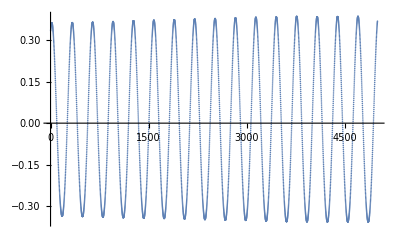

-Graphics-

```mathematica
NewAudio=Re[InverseFourier[CopyEnds[Fourier[Data⟦1⟧],600]]];
ListPlot[ NewAudio⟦20000;;25000⟧]
ListPlay[NewAudio,SampleRate->44100]
```

### Aliasing, Wheels, and video

Regular discrete samples can conflate different frequencies. 
https://www.merriam-webster.com/dictionary/conflate
https://en.wikipedia.org/wiki/Wagon-wheel_effect
https://www.youtube.com/shorts/S4Qi64wTFXA

### Why the DFT works.

In Linear Algebra you learnt how to find the best fit of a linear combination of functions ∑_(i=1)^n a_i p_i(θ) to a bunch of data 
	{{θ_1,x_1},{θ_2,x_2},…,{θ_m,x_m}}
This was over-determined (you could not hit all m points) if m>n which the least squares problem
	A.a≈x
where A was the Tall Skinny matrix 
	A_(i,j)=p_i(θ_j). 
In your Linear Algebra class you typically used polynomials and the data was real.

The Fourier matrix F is what you get with equally spaced angles θ around the unit circle (in the complex plane of course)  and fit powers of the complex exponential ⅇ^(ⅈ k θ)=(ⅇ^(ⅈ θ))^k=cos(k θ)+ⅈ sin(k θ).   The full Fourier matrix hits every data point by reacting to every twitch in the data.

The complex entries in y=F x  are listed from zero wiggles (constant) to one wiggle to two wiggles, to three wiggles etc.

https://www.youtube.com/shorts/S4Qi64wTFXA

The first three terms gives the best fit (in the least squares sense) of the form (y_1(ⅇ^(ⅈ θ)))^0+(y_2(ⅇ^(ⅈ θ)))^1+(y_3(ⅇ^(ⅈ θ)))^2. Unfortunately the coefficients are complex.  The real version looks like the best fit in the span of {1,cos(θ),sin(θ),cos(2θ),sin(2θ),cos(3θ),sin(3θ)}.  Throwing away the middle of the DFT signal removes noise and gives the best fit (in the least squares sense) of a few clean trigonometric polynomials to the data.

### Summary

The DFT of data x∈ℂ^n gives the best fitting linear combinations of a_0+∑_(j=1)^k (a_j cos(j θ)+b_j sin(j θ)) for any j≤n.